NI-DAQ-6000

### Installation

```mathematica
<<NETLink`;
InstallNET[];
$NationalInstrumentsDAQmx = LoadNETAssembly["NationalInstruments.DAQmx","C:\\Program Files (x86)\\National Instruments\\MeasurementStudioVS2010\\DotNET\\Assemblies\\Current\\"];
NETAssembly["NationalInstruments.DAQmx",5];
```

### Device Framework

```mathematica
devOpen[iHandle_]:=Module[
{},
task = NETNew["NationalInstruments.DAQmx.Task"];
termConfig = NETNew["NationalInstruments.DAQmx.AITerminalConfiguration"]@Rse;
aiVolts = NETNew["NationalInstruments.DAQmx.AIVoltageUnits"]@Volts;
task@AIChannels@CreateVoltageChannel[
"Dev1/ai0"(*"Dev1/ai0"*),
"",
termConfig, 
0.0,
5.0,
aiVolts  
];
reader=NETNew["NationalInstruments.DAQmx.AnalogMultiChannelReader",task@Stream];
Return@reader
]

devRead[{iHandle_,dHandle_}]:=dHandle@ReadSingleSample[];
devReadBuffer[{iHandle_,dHandle_},samplenumber_Integer,source_String]:=Return @dHandle@ReadMultiSample[samplenumber];
(*Table[reader@ReadSingleSample[],{10}];
fulldata = reader@ReadMultiSample[1000];
Short[%]
Table[ListPlot[fulldata],{i,1,10}]*)
devReadBuffer[{iHandle_,dHandle_},All,source_String]:= 
devReadBuffer[{iHandle,dHandle},10000,source];
(*usb6000 = devOpen["Dev1/ai0"];
Table[devRead[usb6000],{i,1,10}]*)
```

```mathematica
DeviceFramework`DeviceClassRegister["DAQmx",
"OpenFunction"->devOpen,
(*"WriteFunction"-> K2400Write ,*)
"ReadFunction"-> devRead ,
"ReadBufferFunction"-> devReadBuffer 
(*"CloseFunction"->scopeClose*)
];
```

## NI - DAQ - Test

```mathematica
usb6000 = DeviceOpen["DAQmx"]
```

DeviceObject[…]

```mathematica
(*DeviceRead[usb6000]*)
```

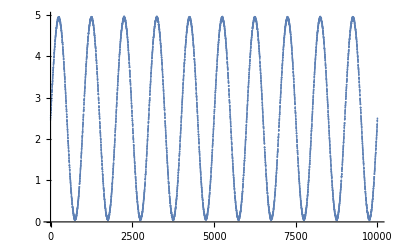

```mathematica
ListPlot[DeviceReadBuffer[usb6000,10000,"source"]]
```

```mathematica
Table[DeviceRead[usb6000],{i,1,10}]
```

{{2.46214},{2.4768},{2.49145},{2.50611},{2.52076},{2.53542},{2.55007},{2.56473},{2.58427},{2.59893}}